# Cosmology PSET 6:

## Problem 1:

```mathematica
vMap=ResourceFunction["ViridisColor"];
```

```mathematica
ode=D[ϵ[t],{t,2}]+(4/(3t)) D[ϵ[t],t]==0;
ϵSol = DSolveValue[ode,ϵ[t],t]
```

-(3 C[1])/t^(1/3)+C[2]

```mathematica
params={Ωd ->5/6,Ωb->1/6};
```

```mathematica
odeD = D[Subscript[δ, d][t],{t,2}]+4/(3 t)D[Subscript[δ, d][t],t] -2/(3 t^2)(Ωd Subscript[δ, d][t]+Ωb Subscript[δ, b][t])==0
```

-(2 (Ωb δ_b[t]+Ωd δ_d[t]))/(3 t^2)+(4 δ_d'[t])/(3 t)+δ_d''[t]==0

```mathematica
odeB = D[Subscript[δ, b][t],{t,2}]+4/(3 t)D[Subscript[δ, b][t],t] -2/(3 t^2)(Ωd Subscript[δ, d][t]+Ωb Subscript[δ, b][t])==0
```

-(2 (Ωb δ_b[t]+Ωd δ_d[t]))/(3 t^2)+(4 δ_b'[t])/(3 t)+δ_b''[t]==0

```mathematica
sysSolution = NDSolveValue[{odeD,odeB, Subscript[δ, d][1]==1*^-3, Subscript[δ, b][1]==1*^-4, Subscript[δ, d]'[1]==0, Subscript[δ, b]'[1]==0}/.params, {Subscript[δ, d],Subscript[δ, b]},{t,1,500}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

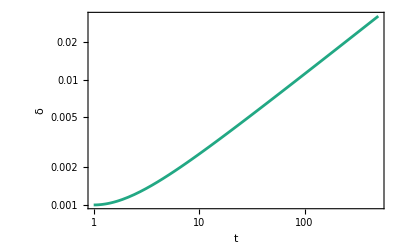

```mathematica
δDPlot = Plot[sysSolution[[1]][t],{t,1,500},  ScalingFunctions->{"Log","Log"}, PlotStyle->vMap[0.6],Frame->True,FrameLabel->{"t", "δ"}]
```

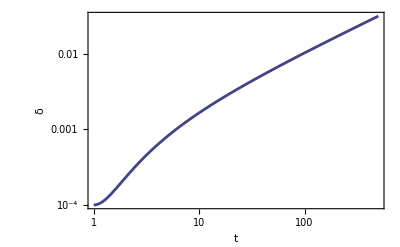

```mathematica
δBPlot =Plot[sysSolution[[2]][t],{t,1,500},  ScalingFunctions->{"Log","Log"}, PlotStyle->vMap[0.2],Frame->True,FrameLabel->{"t", "δ"}]
```

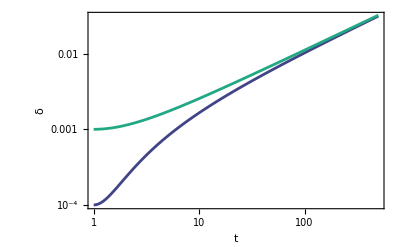

```mathematica
Show[δBPlot ,δDPlot]
```

```mathematica
ratio = (sysSolution[[1]][t])/(sysSolution[[2]][t]);
```

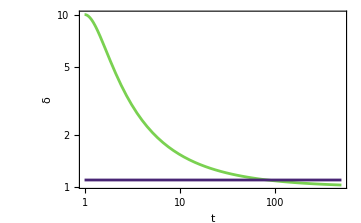

```mathematica
ratioPlot = Plot[{ratio, 1.1},{t,1,500},ScalingFunctions->{"Log","Log"}, PlotStyle->{vMap[0.8],vMap[0.1]} , PlotRange->All,Frame->True, FrameLabel->{"t", "δ"}]
```

```mathematica
tPerturbation = (t/.FindRoot[ratio==1.1, {t,1,500}]) × 380000
```

3.17432×10^7